```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

```mathematica
bold = Style[ #, Bold] &;
fs:= Style[ #, FontSize -> 16 ]&;
```

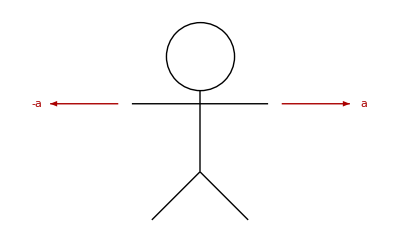

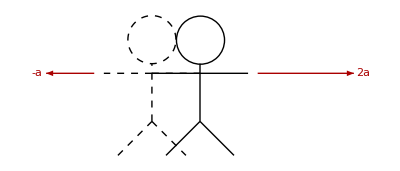

```mathematica
stickpoints::usage = "Return the endpoint coordinates of a stickfigure as:

{leftfoot, pelvis, rightfoot, neckbase, lefthand, righthand, headbase, headcenter, headradii}
";
stickpoints[leglen_, bodylen_, armlen_, necklen_, headradii_, armangle_, legangle_, o_] := Module[{pelvis, neck},
pelvis = leglen{ Sin[legangle], Cos[legangle]};
neck = pelvis +{0,bodylen};
{o, 
o+pelvis,
o+leglen{ 2 Sin[legangle], 0}, 
o+neck, 
o+neck + armlen {-Sin[armangle], -Cos[armangle]}, 
o+neck + armlen { Sin[armangle], -Cos[armangle]}, 
o+neck + {0, necklen},
o+neck + {0, necklen + headradii},
headradii
}
]

stickfigure[{leftfoot_, pelvis_, rightfoot_, neckbase_, lefthand_, righthand_, headbase_, headcenter_, headradii_}, options_] :=  Graphics[Flatten[
{options
,{
Line[{leftfoot, pelvis}]
,Line[{pelvis, rightfoot}]
, Line[{pelvis, headbase}]
, Line[{neckbase, lefthand}]
, Line[{neckbase, righthand}]
, Circle[headbase + {0,headradii}, headradii]
}},1 ]
]

p1 = Module[{pts, left, right, aoff, adir},
pts = stickpoints[1, 1, 1, 0.2, 0.5, Pi/2, Pi/4, {-1,0}];
left = pts[[5]];
right = pts[[6]];
aoff = {0.2,0};
adir = {1,0};
Show[{
(*Plot[0,{x,-3,3}, PlotRange -> {{-3,3},{-3,3}}, AspectRatio->1]
,*)
stickfigure[pts, {Thick}]
, Graphics[{
Thick,
Red // Darker,

Arrow[ {left - aoff, left - aoff - adir}],
Arrow[ {right + aoff, right + aoff + adir}],
Text[Row[{(*"" //fs,*) "a" //fs//bold}],  right + aoff + 1.2adir],
Text[Row[{"-" //fs, "a" //fs//bold}],  left - aoff -1.2 adir]
}]

}
]
]

p2 = Module[{pts, left, right, right2, aoff, adir, pts2},
pts = stickpoints[1, 1, 1, 0.2, 0.5, Pi/2, Pi/4, {0,0}];
pts2= stickpoints[1, 1, 1, 0.2, 0.5, Pi/2, Pi/4, {1,0}];
left = pts[[5]];
right = pts[[6]];
right2 = pts2[[6]];
aoff = {0.2,0};
adir = {1,0};
Show[{

stickfigure[pts, {Dashed}],
stickfigure[pts2, {Thick}]
, Graphics[{
Thick,
Red // Darker,

Arrow[ {left - aoff, left - aoff - adir}],
Arrow[ {right2 + aoff, right2+ aoff + 2adir}],
Text[Row[{"2" //fs, "a" //fs//bold}],  right2 + aoff + 2.2adir],
Text[Row[{"-" //fs, "a" //fs//bold}],  left - aoff -1.2 adir]
}]

}
]
]
```

```mathematica
peeters`exportForLatex["equalForcesFig1", p1]
peeters`exportForLatex["unequalForcesFig2", p2]
```

{equalForcesFig1.eps,equalForcesFig1pn.png}

{unequalForcesFig2.eps,unequalForcesFig2pn.png}